# Notebook for : Electrodynamics in the Friedmann–Robertson–Walker universe: Maxwell and Dirac fields in Newman–Penrose formalism by Khanal

Geoff Cope
University of Utah
March 7, 2021

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Article

```mathematica
Hyperlink["Electrodynamics in the Friedmann–Robertson–Walker universe: Maxwell and Dirac fields in Newman–Penrose formalism by  Khanal",
"https://arxiv.org/abs/astro-ph/0508566"]
```

[Electrodynamics in the Friedmann–Robertson–Walker universe: Maxwell and Dirac fields in Newman–Penrose formalism by  Khanal](https://arxiv.org/abs/astro-ph/0508566)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 660 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,VariationalMethods`,GeneralRelativityTensors`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"]
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv ,
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z]-> dz , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[ϱ]-> dϱ , 
Dt[φ] -> dφ ,
Dt[ξ]-> dξ ,  
 Dt[𝓉] -> d𝓉 , 
Dt[𝓋]-> d𝓋 , 
Dt[𝓊]-> d𝓊 ,
Dt[𝓍]-> d𝓍 ,
Dt[𝓎]-> d𝓎,   
Dt[𝓏] -> d𝓏,
Dt[T]-> dT,
Dt[X]-> dX, 
Dt[Y]-> dY,
Dt[Z]-> dZ,
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ , 
Dt[ζ]-> dζ , 
Dt[ζbar]-> dζbar 
};
dtReplace // TableForm
```

Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[ϱ]→dϱ
Dt[φ]→dφ
Dt[ξ]→dξ
Dt[𝓉]→d𝓉
Dt[𝓋]→d𝓋
Dt[𝓊]→d𝓊
Dt[𝓍]→d𝓍
Dt[𝓎]→d𝓎
Dt[𝓏]→d𝓏
Dt[T]→dT
Dt[X]→dX
Dt[Y]→dY
Dt[Z]→dZ
Dt[U]→dU
Dt[V]→dV
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ
Dt[ζ]→dζ
Dt[ζbar]→dζbar

```mathematica
a/:Dt[a]=0  ;  
M /: Dt[M] = 0 ;
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 4

```mathematica
Clear[eq2]
eq2 = 
a[η]^2( dη^2- (1/f[r]^2)(dr^2+ r^2(dθ^2+ Sin[θ]^2 dϕ^2)))
```

a[η]^2 (dη^2-(dr^2+r^2 (dθ^2+dϕ^2 Sin[θ]^2))/f[r]^2)

```mathematica
Clear[metric2]
metric2 = 
lineToMetric[ eq2 , {dη,dr,dθ,dϕ}]  ;
metric2 // MatrixForm
```

(a[η]^2 | 0 | 0 | 0
0 | -a[η]^2/f[r]^2 | 0 | 0
0 | 0 | -(r^2 a[η]^2)/f[r]^2 | 0
0 | 0 | 0 | -(r^2 a[η]^2 Sin[θ]^2)/f[r]^2)

```mathematica
Clear[inverse2]
inverse2 = 
Inverse[metric2] // Expand // Simplify  ;
inverse2 // MatrixForm
```

(1/a[η]^2 | 0 | 0 | 0
0 | -f[r]^2/a[η]^2 | 0 | 0
0 | 0 | -f[r]^2/(r^2 a[η]^2) | 0
0 | 0 | 0 | -(Csc[θ]^2 f[r]^2)/(r^2 a[η]^2))

## Tensors Calculated For Metric 4

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ; 
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
 tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 9,15 for all tensors *) 
input[ "metric2", metric2, "FRLW","g^FRLW",{η,r,θ,ϕ}, "Greek"] // Timing
```

{9.35854,Null}

```mathematica
tensorList
```

{(g^FRLW)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList[[1]] 
TensorName[tensorList[[1]]] 
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(g^FRLW)_αβ^

FRLW

((a(η))^2 | 0 | 0 | 0
0 | -(a(η))^2/(f(r))^2 | 0 | 0
0 | 0 | -(r^2 (a(η))^2)/(f(r))^2 | 0
0 | 0 | 0 | -(r^2 (a(η))^2 sin^2(θ))/(f(r))^2)

```mathematica
tensorList[[2]] 
TensorName[tensorList[[2]]] 
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolFRLW

((((∂a(η))/(∂η))/(a(η))
0
0
0) | (0
((∂a(η))/(∂η))/(a(η) (f(r))^2)
0
0) | (0
0
(r^2 (∂a(η))/(∂η))/(a(η) (f(r))^2)
0) | (0
0
0
(r^2 sin^2(θ) (∂a(η))/(∂η))/(a(η) (f(r))^2))
(0
((∂a(η))/(∂η))/(a(η))
0
0) | (((∂a(η))/(∂η))/(a(η))
-((∂f(r))/(∂r))/(f(r))
0
0) | (0
0
r ((r (∂f(r))/(∂r))/(f(r))-1)
0) | (0
0
0
(r sin^2(θ) (r (∂f(r))/(∂r)-f(r)))/(f(r)))
(0
0
((∂a(η))/(∂η))/(a(η))
0) | (0
0
1/r-((∂f(r))/(∂r))/(f(r))
0) | (((∂a(η))/(∂η))/(a(η))
1/r-((∂f(r))/(∂r))/(f(r))
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
((∂a(η))/(∂η))/(a(η))) | (0
0
0
1/r-((∂f(r))/(∂r))/(f(r))) | (0
0
0
cot(θ)) | (((∂a(η))/(∂η))/(a(η))
1/r-((∂f(r))/(∂r))/(f(r))
cot(θ)
0))

```mathematica
tensorList[[3]] 
TensorName[tensorList[[3]]] 
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorFRLW

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2)/(f(r))^2 | 0 | 0
-(a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2)/(f(r))^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (r^2 (a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2))/(f(r))^2 | 0
0 | 0 | 0 | 0
-(r^2 (a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2))/(f(r))^2 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(r^2 sin^2(θ) (((∂a(η))/(∂η))^2-a(η) (∂^2 a(η))/(∂η^2)))/(f(r))^2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(r^2 sin^2(θ) (((∂a(η))/(∂η))^2-a(η) (∂^2 a(η))/(∂η^2)))/(f(r))^2 | 0 | 0 | 0)
(0 | -(a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2)/(f(r))^2 | 0 | 0
(a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2)/(f(r))^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(r ((a(η))^2 (f(r) (r (∂^2 f(r))/(∂r^2)+(∂f(r))/(∂r))-r ((∂f(r))/(∂r))^2)+r ((∂a(η))/(∂η))^2))/(f(r))^4 | 0
0 | (r ((a(η))^2 (f(r) (r (∂^2 f(r))/(∂r^2)+(∂f(r))/(∂r))-r ((∂f(r))/(∂r))^2)+r ((∂a(η))/(∂η))^2))/(f(r))^4 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(r sin^2(θ) ((a(η))^2 (f(r) (r (∂^2 f(r))/(∂r^2)+(∂f(r))/(∂r))-r ((∂f(r))/(∂r))^2)+r ((∂a(η))/(∂η))^2))/(f(r))^4
0 | 0 | 0 | 0
0 | (r sin^2(θ) ((a(η))^2 (f(r) (r (∂^2 f(r))/(∂r^2)+(∂f(r))/(∂r))-r ((∂f(r))/(∂r))^2)+r ((∂a(η))/(∂η))^2))/(f(r))^4 | 0 | 0)
(0 | 0 | -(r^2 (a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2))/(f(r))^2 | 0
0 | 0 | 0 | 0
(r^2 (a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2))/(f(r))^2 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (r ((a(η))^2 (f(r) (r (∂^2 f(r))/(∂r^2)+(∂f(r))/(∂r))-r ((∂f(r))/(∂r))^2)+r ((∂a(η))/(∂η))^2))/(f(r))^4 | 0
0 | -(r ((a(η))^2 (f(r) (r (∂^2 f(r))/(∂r^2)+(∂f(r))/(∂r))-r ((∂f(r))/(∂r))^2)+r ((∂a(η))/(∂η))^2))/(f(r))^4 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(r^3 sin^2(θ) ((a(η))^2 (∂f(r))/(∂r) (2 f(r)-r (∂f(r))/(∂r))+r ((∂a(η))/(∂η))^2))/(f(r))^4
0 | 0 | (r^3 sin^2(θ) ((a(η))^2 (∂f(r))/(∂r) (2 f(r)-r (∂f(r))/(∂r))+r ((∂a(η))/(∂η))^2))/(f(r))^4 | 0)
(0 | 0 | 0 | (r^2 sin^2(θ) (((∂a(η))/(∂η))^2-a(η) (∂^2 a(η))/(∂η^2)))/(f(r))^2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(r^2 sin^2(θ) (((∂a(η))/(∂η))^2-a(η) (∂^2 a(η))/(∂η^2)))/(f(r))^2 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (r sin^2(θ) ((a(η))^2 (f(r) (r (∂^2 f(r))/(∂r^2)+(∂f(r))/(∂r))-r ((∂f(r))/(∂r))^2)+r ((∂a(η))/(∂η))^2))/(f(r))^4
0 | 0 | 0 | 0
0 | -(r sin^2(θ) ((a(η))^2 (f(r) (r (∂^2 f(r))/(∂r^2)+(∂f(r))/(∂r))-r ((∂f(r))/(∂r))^2)+r ((∂a(η))/(∂η))^2))/(f(r))^4 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (r^3 sin^2(θ) ((a(η))^2 (∂f(r))/(∂r) (2 f(r)-r (∂f(r))/(∂r))+r ((∂a(η))/(∂η))^2))/(f(r))^4
0 | 0 | -(r^3 sin^2(θ) ((a(η))^2 (∂f(r))/(∂r) (2 f(r)-r (∂f(r))/(∂r))+r ((∂a(η))/(∂η))^2))/(f(r))^4 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[4]] 
TensorName[tensorList[[4]]] 
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorFRLW

((3 (((∂a(η))/(∂η))^2-a(η) (∂^2 a(η))/(∂η^2)))/(a(η))^2 | 0 | 0 | 0
0 | (a(η) (2 a(η) (f(r) (r (∂^2 f(r))/(∂r^2)+(∂f(r))/(∂r))-r ((∂f(r))/(∂r))^2)+r (∂^2 a(η))/(∂η^2))+r ((∂a(η))/(∂η))^2)/(r (a(η))^2 (f(r))^2) | 0 | 0
0 | 0 | (r (a(η) (a(η) (r f(r) (∂^2 f(r))/(∂r^2)-2 r ((∂f(r))/(∂r))^2+3 f(r) (∂f(r))/(∂r))+r (∂^2 a(η))/(∂η^2))+r ((∂a(η))/(∂η))^2))/((a(η))^2 (f(r))^2) | 0
0 | 0 | 0 | (r sin^2(θ) (a(η) (a(η) (r f(r) (∂^2 f(r))/(∂r^2)-2 r ((∂f(r))/(∂r))^2+3 f(r) (∂f(r))/(∂r))+r (∂^2 a(η))/(∂η^2))+r ((∂a(η))/(∂η))^2))/((a(η))^2 (f(r))^2))

```mathematica
tensorList[[5]] 
TensorName[tensorList[[5]]] 
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

R

RicciScalarFRLW

(a(η) (6 r ((∂f(r))/(∂r))^2-4 f(r) (r (∂^2 f(r))/(∂r^2)+2 (∂f(r))/(∂r)))-6 r (∂^2 a(η))/(∂η^2))/(r (a(η))^3)

```mathematica
tensorList[[6]] 
TensorName[tensorList[[6]]] 
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarFRLW

1/(r^2 (a(η))^8)4 (2 r a(η) ((∂a(η))/(∂η))^2 (a(η) (2 r f(r) (∂^2 f(r))/(∂r^2)-3 r ((∂f(r))/(∂r))^2+4 f(r) (∂f(r))/(∂r))-3 r (∂^2 a(η))/(∂η^2))+(a(η))^4 (-4 r f(r) (r (∂^2 f(r))/(∂r^2)+2 (∂f(r))/(∂r)) ((∂f(r))/(∂r))^2+2 (f(r))^2 (2 r (∂^2 f(r))/(∂r^2) (∂f(r))/(∂r)+r^2 ((∂^2 f(r))/(∂r^2))^2+3 ((∂f(r))/(∂r))^2)+3 r^2 ((∂f(r))/(∂r))^4)+3 r^2 (a(η))^2 ((∂^2 a(η))/(∂η^2))^2+6 r^2 ((∂a(η))/(∂η))^4)

```mathematica
tensorList[[7]] 
TensorName[tensorList[[7]]] 
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorFRLW

((3 ((∂a(η))/(∂η))^2)/(a(η))^2+f(r) (2 (∂^2 f(r))/(∂r^2)+(4 (∂f(r))/(∂r))/r)-3 ((∂f(r))/(∂r))^2 | 0 | 0 | 0
0 | (a(η) (a(η) (∂f(r))/(∂r) (r (∂f(r))/(∂r)-2 f(r))-2 r (∂^2 a(η))/(∂η^2))+r ((∂a(η))/(∂η))^2)/(r (a(η))^2 (f(r))^2) | 0 | 0
0 | 0 | (r (r ((∂a(η))/(∂η))^2-a(η) (a(η) (f(r) (r (∂^2 f(r))/(∂r^2)+(∂f(r))/(∂r))-r ((∂f(r))/(∂r))^2)+2 r (∂^2 a(η))/(∂η^2))))/((a(η))^2 (f(r))^2) | 0
0 | 0 | 0 | (r sin^2(θ) (r ((∂a(η))/(∂η))^2-a(η) (a(η) (f(r) (r (∂^2 f(r))/(∂r^2)+(∂f(r))/(∂r))-r ((∂f(r))/(∂r))^2)+2 r (∂^2 a(η))/(∂η^2))))/((a(η))^2 (f(r))^2))

```mathematica
tensorList[[8]] 
TensorName[tensorList[[8]]] 
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorFRLW

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ((a(η))^2 ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(3 r f(r)) | 0 | 0
((a(η))^2 (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(3 r f(r)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (r (a(η))^2 (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(6 f(r)) | 0
0 | 0 | 0 | 0
(r (a(η))^2 ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(6 f(r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (r (a(η))^2 sin^2(θ) (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(6 f(r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(r (a(η))^2 sin^2(θ) ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(6 f(r)) | 0 | 0 | 0)
(0 | ((a(η))^2 (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(3 r f(r)) | 0 | 0
((a(η))^2 ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(3 r f(r)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (r (a(η))^2 ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(6 (f(r))^3) | 0
0 | (r (a(η))^2 (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(6 (f(r))^3) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (r (a(η))^2 sin^2(θ) ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(6 (f(r))^3)
0 | 0 | 0 | 0
0 | (r (a(η))^2 sin^2(θ) (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(6 (f(r))^3) | 0 | 0)
(0 | 0 | (r (a(η))^2 ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(6 f(r)) | 0
0 | 0 | 0 | 0
(r (a(η))^2 (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(6 f(r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (r (a(η))^2 (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(6 (f(r))^3) | 0
0 | (r (a(η))^2 ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(6 (f(r))^3) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (r^3 (a(η))^2 sin^2(θ) (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(3 (f(r))^3)
0 | 0 | (r^3 (a(η))^2 sin^2(θ) ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(3 (f(r))^3) | 0)
(0 | 0 | 0 | (r (a(η))^2 sin^2(θ) ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(6 f(r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(r (a(η))^2 sin^2(θ) (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(6 f(r)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (r (a(η))^2 sin^2(θ) (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(6 (f(r))^3)
0 | 0 | 0 | 0
0 | (r (a(η))^2 sin^2(θ) ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(6 (f(r))^3) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (r^3 (a(η))^2 sin^2(θ) ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(3 (f(r))^3)
0 | 0 | (r^3 (a(η))^2 sin^2(θ) (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(3 (f(r))^3) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[9]] 
TensorName[tensorList[[9]]] 
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorFRLW

((0
(4 r (∂f(r))/(∂r) ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2))+f(r) (2 r (2 (∂^2 f(r))/(∂r^2)+r (∂^3 f(r))/(∂r^3))-4 (∂f(r))/(∂r)))/(3 r^2)
0
0) | ((4 r (∂f(r))/(∂r) (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r))+f(r) (4 (∂f(r))/(∂r)-2 r (2 (∂^2 f(r))/(∂r^2)+r (∂^3 f(r))/(∂r^3))))/(3 r^2)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
(2 (∂a(η))/(∂η) (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(3 r a(η) f(r))
0
0) | ((2 (∂a(η))/(∂η) ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(3 r a(η) f(r))
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
(r (∂a(η))/(∂η) ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(3 a(η) f(r))
0) | (0
0
-(2 r (∂f(r))/(∂r) ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2))+f(r) (r (2 (∂^2 f(r))/(∂r^2)+r (∂^3 f(r))/(∂r^3))-2 (∂f(r))/(∂r)))/(3 (f(r))^2)
0) | ((r (∂a(η))/(∂η) (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(3 a(η) f(r))
(2 r (∂f(r))/(∂r) ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2))+f(r) (r (2 (∂^2 f(r))/(∂r^2)+r (∂^3 f(r))/(∂r^3))-2 (∂f(r))/(∂r)))/(3 (f(r))^2)
0
0) | (0
0
0
0)
(0
0
0
(r sin^2(θ) (∂a(η))/(∂η) ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2)))/(3 a(η) f(r))) | (0
0
0
(sin^2(θ) (2 r (∂f(r))/(∂r) (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r))+f(r) (2 (∂f(r))/(∂r)-r (2 (∂^2 f(r))/(∂r^2)+r (∂^3 f(r))/(∂r^3)))))/(3 (f(r))^2)) | (0
0
0
0) | ((r sin^2(θ) (∂a(η))/(∂η) (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(3 a(η) f(r))
(sin^2(θ) (2 r (∂f(r))/(∂r) ((∂f(r))/(∂r)-r (∂^2 f(r))/(∂r^2))+f(r) (r (2 (∂^2 f(r))/(∂r^2)+r (∂^3 f(r))/(∂r^3))-2 (∂f(r))/(∂r))))/(3 (f(r))^2)
0
0))

## Null Tetrad Construction and Check of Orthogonality

```mathematica
Clear[ℓ]
ℓ=
{1,-1/f[r],0,0}
```

{1,-1/f[r],0,0}

```mathematica
Clear[𝓃]
𝓃 = 
(a[η]^2/2){1,1/f[r],0,0}
```

{a[η]^2/2,a[η]^2/(2 f[r]),0,0}

```mathematica
Clear[𝓂]
𝓂 = 
((-a[η] r)/(√2 f[r])){0,0,-1,-ⅈ Sin[θ] }
```

{0,0,(r a[η])/(√2 f[r]),(ⅈ r a[η] Sin[θ])/(√2 f[r])}

```mathematica
Clear[𝓂bar]
𝓂bar =
((-a[η] r)/(√2 f[r])){0,0,-1,+ⅈ Sin[θ] }
```

{0,0,(r a[η])/(√2 f[r]),-(ⅈ r a[η] Sin[θ])/(√2 f[r])}

```mathematica
(* Always check if indices needed are up or down and these are DOWN *) 
l = ToTensor[ {"NewTensor" , "l"} , tensorList[[1]] , ℓ , {-μ}]
n = ToTensor[{"NewTensor" , "n" } , tensorList[[1]] , 𝓃 , {-μ} ] 
m = ToTensor[{"NewTensor" , "m" } , tensorList[[1]] , 𝓂 , {-μ} ] 
mbar = ToTensor[{"NewTensor" , "mbar" } , tensorList[[1]] , 𝓂bar , {-μ} ]
```

l_μ^

n_μ^

m_μ^

mbar_μ^

```mathematica
TensorValues[ContractIndices[l[-μ]l[μ]]] == 0  // Expand // Simplify 
TensorValues[ContractIndices[n[-μ]n[μ]] ]== 0   // Expand // Simplify 
TensorValues[ContractIndices[m[-μ]m[μ]]] == 0   // Expand // FullSimplify 
TensorValues[ContractIndices[mbar[-μ]mbar[μ]]] == 0  // Expand // FullSimplify 
TensorValues[ContractIndices[l[-μ]n[μ]]] == 1// Expand // FullSimplify 
TensorValues[ContractIndices[l[μ]n[-μ]]] == 1  // Expand // FullSimplify 
TensorValues[ContractIndices[m[-μ]mbar[μ]]] == - 1 // Expand // FullSimplify 
TensorValues[ContractIndices[m[μ]mbar[-μ]]] == - 1 // Expand // FullSimplify 
Clear[completenessDownIndices]
completenessDownIndices = 
MergeTensors[l[-μ]n[-ν]+n[-μ]l[-ν] - m[-μ]mbar[-ν]- m[-ν]mbar[-μ]]  ;
TensorValues[ completenessDownIndices ]   // Expand // FullSimplify // MatrixForm

Thread[Flatten[metric2] == 
Flatten[ TensorValues[ completenessDownIndices ]] ] // Expand // FullSimplify  // TableForm

Clear[completenessUpIndices]
completenessUpIndices = 
MergeTensors[l[μ]n[ν]+n[μ]l[ν] - m[μ]mbar[ν]- m[ν]mbar[μ]]  ;
TensorValues[ completenessUpIndices ]   // Expand // FullSimplify // MatrixForm

Thread[Flatten[inverse2] == 
Flatten[ TensorValues[ completenessUpIndices ]] ]  // Expand // FullSimplify  // TableForm
```

True

True

True

«5 more identical outputs»

(a[η]^2 | 0 | 0 | 0
0 | -a[η]^2/f[r]^2 | 0 | 0
0 | 0 | -(r^2 a[η]^2)/f[r]^2 | 0
0 | 0 | 0 | -(r^2 a[η]^2 Sin[θ]^2)/f[r]^2)

True

(1/a[η]^2 | 0 | 0 | 0
0 | -f[r]^2/a[η]^2 | 0 | 0
0 | 0 | -f[r]^2/(r^2 a[η]^2) | 0
0 | 0 | 0 | -(Csc[θ]^2 f[r]^2)/(r^2 a[η]^2))

True

## Newman Penrose Quantities Calculated For Metric 4

```mathematica
Clear[spinCoefficientReplace] 
spinCoefficientReplace= {
α-> ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ] mbar[ν]] // TensorValues )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] mbar[ν]] // TensorValues)) ) , 
β -> 
((1/2)((MergeTensors[ CovariantD[ l[-μ],-ν] n[μ]m[ν]] // TensorValues)- 
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] m[ν]] // TensorValues ))),
γ -> (* something weird here correct definition off by minus sign *) ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ]n[ν] ] // TensorValues  // Expand  )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] n[ν]] // TensorValues // Expand  // FullSimplify )) // Expand ) , 
ε -> ( (1/2)(( MergeTensors[CovariantD[l[-μ],-ν] n[μ] l[ν]] // TensorValues  // Expand  // FullSimplify  )  - 
(MergeTensors[ CovariantD[ m[-μ],-ν] mbar[μ] l[ν]] // TensorValues // Expand // FullSimplify) ) // Expand  // FullSimplify ) , 
κ->(  MergeTensors[ CovariantD[ l[-μ] ,-ν] m[μ] l[ν]  ]  // TensorValues ) , 
λ-> (* note minus sign *)(-1)*( MergeTensors[ CovariantD[ n[-μ],-ν] mbar[μ] mbar[ν] ]  // TensorValues // Expand // FullSimplify)  ,
μ-> (*note minus sign *)(-1)*( MergeTensors [ CovariantD[ n[-μ] , -ν ] mbar[μ] m[ν] ] // TensorValues  // Expand  // FullSimplify )  , 
ν-> ( MergeTensors[ CovariantD[ n[-μ],-ν]m[μ] n[ν] ] // TensorValues ) , 
π-> (* Note minus sign *)(-1)* (MergeTensors[CovariantD[ n[-μ],-ν] mbar[μ] l[ν]] // TensorValues  // Expand ) , 
ρ ->(  MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] mbar[ν] ] // TensorValues  // Expand // FullSimplify )  , σ->( MergeTensors[ CovariantD[l[-μ] , -ν] m[μ] m[ν]] // TensorValues  // Expand // FullSimplify)  , 
τ->( MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] n[ν ]]// TensorValues )   
} ;
spinCoefficientReplace   // TableForm // pdConv
```

α→(f(r) cot(θ))/(2 √2 r a(η))
β→-(f(r) cot(θ))/(2 √2 r a(η))
γ→-((∂a(η))/(∂η))/(2 a(η))
ε→0
κ→0
λ→0
μ→1/2 (((∂a(η))/(∂η))/(a(η))-(f(r))/r+(∂f(r))/(∂r))
ν→0
π→0
ρ→-(a(η) f(r)-r a(η) (∂f(r))/(∂r)+r (∂a(η))/(∂η))/(r (a(η))^3)
σ→0
τ→0

```mathematica
Clear[ricciScalarsReplace] 
ricciScalarsReplace = {
Subscript[Φ, OO]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]l[ν]]] // Expand // FullSimplify,
Subscript[Φ, O1]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]m[ν]]] // Expand // FullSimplify,
Subscript[Φ, O2]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]m[μ]m[ν]]] // Expand // FullSimplify,

Subscript[Φ, 10]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]mbar[ν]]]  // Expand // Simplify ,
Subscript[Φ, 11]-> 
(-1/4)*( ( TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]n[ν]]])+ (TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]m[μ]mbar[ν]]])) // Expand // FullSimplify,
Subscript[Φ, 12]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]m[ν]]] // Expand // FullSimplify,
Subscript[Φ, 20]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]mbar[μ]mbar[ν]]]// Expand // Simplify ,
Subscript[Φ, 21]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]mbar[ν]]]  // Expand // Simplify ,
Subscript[Φ, 22]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]n[ν]]]// Expand // FullSimplify ,
Λ-> 
(1/24)*TensorValues[tensorList[[5]]]// Expand // FullSimplify
};
ricciScalarsReplace   // TableForm // pdConv
```

Φ_OO→(a(η) (a(η) (r ((∂f(r))/(∂r))^2-f(r) (r (∂^2 f(r))/(∂r^2)+(∂f(r))/(∂r)))+r (∂^2 a(η))/(∂η^2))-2 r ((∂a(η))/(∂η))^2)/(r (a(η))^6)
Φ_O1→0
Φ_O2→0
Φ_10→0
Φ_11→(a(η) (a(η) (∂f(r))/(∂r) (r (∂f(r))/(∂r)-2 f(r))+r (∂^2 a(η))/(∂η^2))-2 r ((∂a(η))/(∂η))^2)/(4 r (a(η))^4)
Φ_12→0
Φ_20→0
Φ_21→0
Φ_22→1/4 ((a(η) (∂^2 a(η))/(∂η^2)-2 ((∂a(η))/(∂η))^2)/(a(η))^2-(f(r) (r (∂^2 f(r))/(∂r^2)+(∂f(r))/(∂r)))/r+((∂f(r))/(∂r))^2)
Λ→(a(η) (3 r ((∂f(r))/(∂r))^2-2 f(r) (r (∂^2 f(r))/(∂r^2)+2 (∂f(r))/(∂r)))-3 r (∂^2 a(η))/(∂η^2))/(12 r (a(η))^3)

```mathematica
Clear[weylScalarsReplace](* Definitions from Griffiths *) 
weylScalarsReplace = {

   Subscript[Ψ, 0]-> 
(-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]l[μ]m[ν]]]// Expand // FullSimplify , 
	 Subscript[Ψ, 1]-> 
(-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]n[λ]l[μ]m[ν]]]// Expand // FullSimplify , 
	 Subscript[Ψ, 2]-> 
(-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]mbar[μ]n[ν]]] // Expand // FullSimplify, 
	 Subscript[Ψ, 3]-> 
(-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]n[κ]l[λ]n[μ]mbar[ν]]]// Expand // FullSimplify , 
	 Subscript[Ψ, 4]-> 
(-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]n[κ]mbar[λ]n[μ]mbar[ν]]]// Expand // FullSimplify
} ;
weylScalarsReplace  // TableForm // pdConv
```

Ψ_0→0
Ψ_1→0
Ψ_2→(f(r) (r (∂^2 f(r))/(∂r^2)-(∂f(r))/(∂r)))/(6 r (a(η))^2)
Ψ_3→0
Ψ_4→0

```mathematica
Clear[eq11,l] (* Hugely confusing figure out workaround. l is null vector and eigenvalue parameter *) 
eq11 = {
V-> l(l+1)r^2, 
V-> l(l+1) Sin[𝓇]^2 , 
V-> l(l+1) Sinh[𝓇]^2
} ;
eq11 // TableForm
```

V→l (1+l) r^2
V→l (1+l) Sin[𝓇]^2
V→l (1+l) Sinh[𝓇]^2

```mathematica
Clear[eq10]
eq10 = 
D[R[r],{r,2}] + ω^2 R[r] == V R[r]
```

ω^2 R[r]+R''[r]==V R[r]

```mathematica
eq10 /. eq11[[1]]
eq10 /. eq11[[2]]
eq10 /. eq11[[3]]
```

ω^2 R[r]+R''[r]==l (1+l) r^2 R[r]

ω^2 R[r]+R''[r]==l (1+l) R[r] Sin[𝓇]^2

ω^2 R[r]+R''[r]==l (1+l) R[r] Sinh[𝓇]^2

```mathematica
Plot[
Evaluate[
R[r] /.( Flatten[DSolve[ ( eq10 /. eq11[[1]]) , R[r],r]] /. C[1]-> 1 /. C[2]-> 1  /. l-> 1  /. ω-> 1 ) ] , {r,1,5}]
```

-Graphics-

```mathematica
R[r] /.( Flatten[DSolve[ ( eq10 /. eq11[[1]]) , R[r],r]] /. C[1]-> 1 /. C[2]-> 1  /. l-> 1  /. ω-> 1 )
```

ParabolicCylinderD[(-1-√2)/(2 √2),ⅈ 2^(3/4) r]+ParabolicCylinderD[(1-√2)/(2 √2),2^(3/4) r]

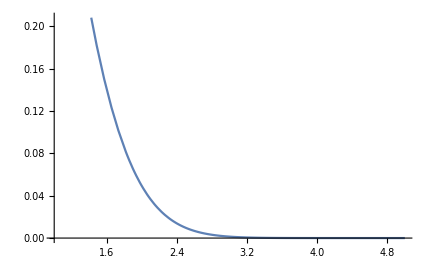

```mathematica
Plot[ParabolicCylinderD[(1-√2)/(2 √2),2^(3/4) r] , {r,1,5}]
```

```mathematica
?ParabolicCylinderD
```